# Approximate expressions for the escape energy

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new

Here we obtain approximate expressions for the escape energy using the data obtained from “EscapeEnergyData.nb”. The data are located in “E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData”. We try to fit the data to the expression ε(ρ_0)=a+b/ρ_0+c/ρ_0^2.

## Positive l

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\PositiveL"}]
```

{E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b01EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b02EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b03EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b04EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b05EscEdat.mx}

```mathematica
data=Import[#]&/@files;
```

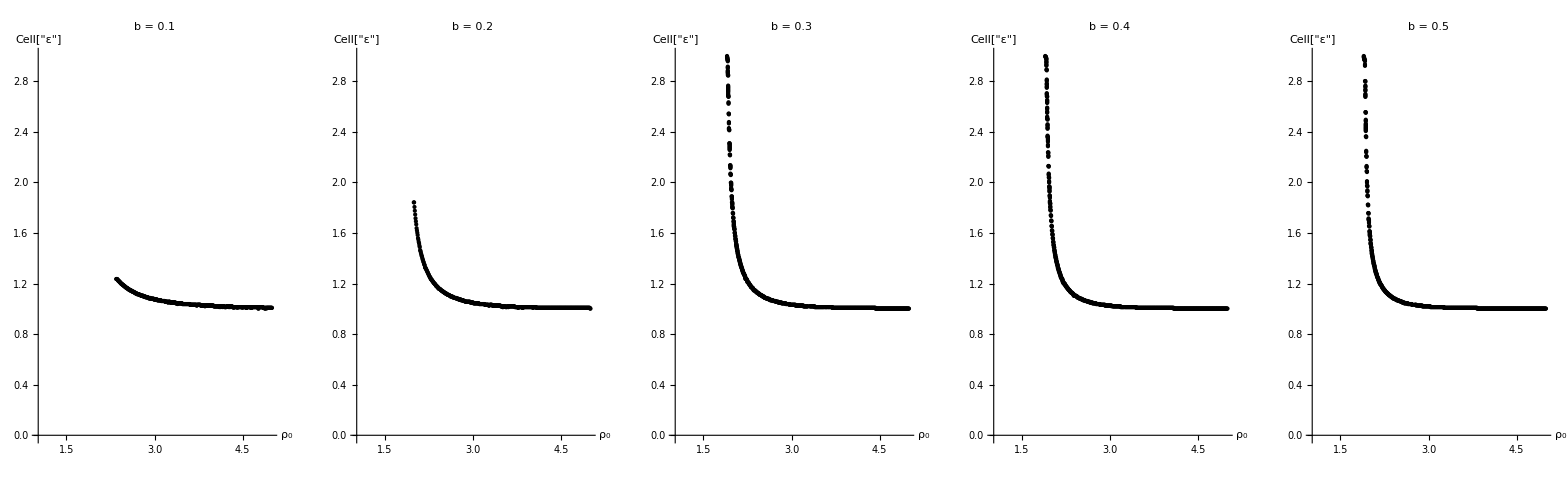

```mathematica
GraphicsRow[Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{0,3}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"1f9a1c9e-ea09-41db-951b-ec84cca67e80"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->Automatic],{i,1,5}]]
```

```mathematica
dataPlot=Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{0,3}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"0d5d9110-0168-4d6c-bdf8-486c77f7799f"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->Automatic],{i,1,5}];
```

```mathematica
plotColors={Red,Green,Blue,Yellow,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0.5, 0, 0.5]}

```mathematica
eqn=Table[1+a/(x-r)/.FindFit[data⟦i⟧,1+a/(x-r),{a,,r},x],{i,1,5}];
```

```mathematica
eqnPlot=Table[Plot[eqn⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

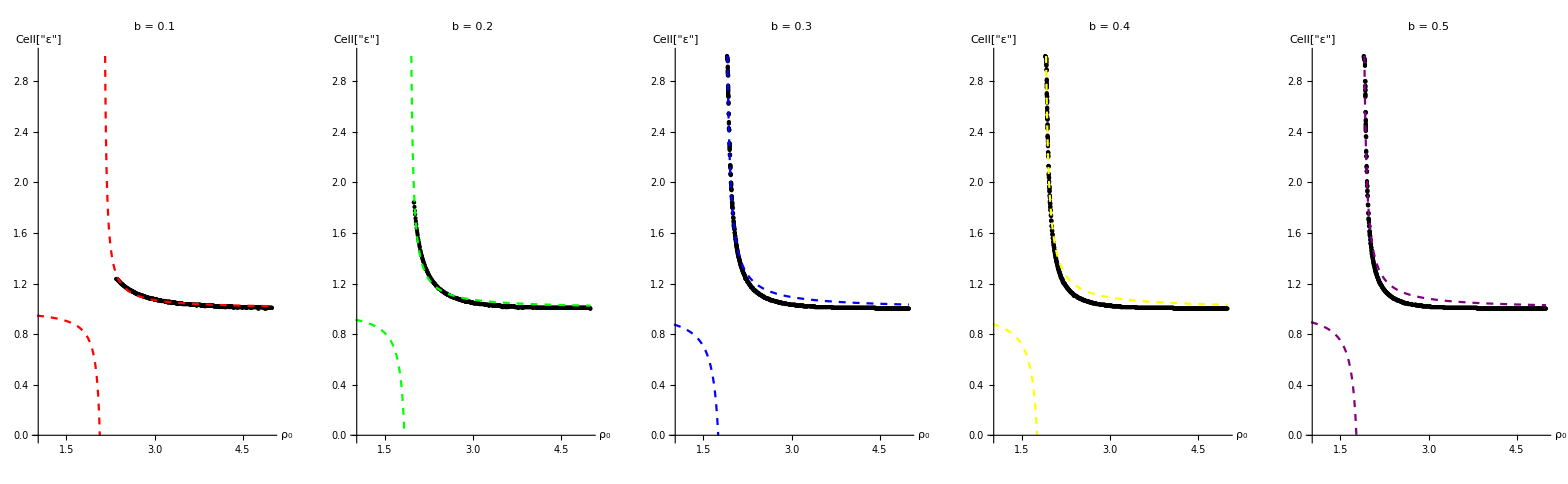

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqnPlot⟦i⟧],{i,1,5}]]
```

```mathematica
eqn1=Table[Fit[data⟦i⟧,{1,1/x,1/x^2},x],{i,1,5}];
```

```mathematica
eqn1Plot=Table[Plot[eqn1⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

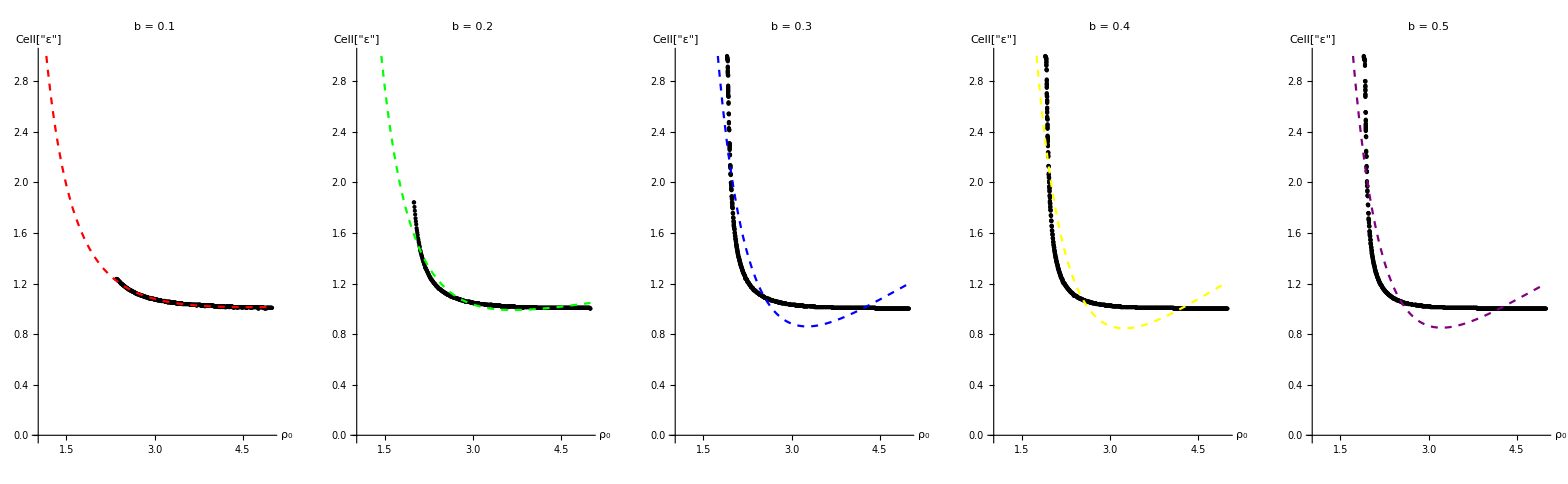

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn1Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Export["escEplb0"<>ToString[i],Show[dataPlot⟦i⟧,eqn1Plot⟦i⟧]]
]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn⟦i⟧]
]
```

b = 0.1:  (1.23458+4.74179/x^2-2.04749/x)

b = 0.2:  (1.81053+11.1806/x^2-6.05477/x)

b = 0.3:  (3.68224+30.1035/x^2-18.432/x)

b = 0.4:  (3.80872+31.1356/x^2-19.2097/x)

b = 0.5:  (3.62106+28.8071/x^2-17.8667/x)

We see from above that the fit is not accurate for positive l.

We have good reasons to believe that the escape energy for the case of positive l asymptotes to 1, i.e. ε_esc→ 1 as ρ_0→ ∞. We try to fit this set of data to the expression  ε_esc= 1+a ρ_0^-b.

```mathematica
eqn2=Table[1+a x^-b/.FindFit[data⟦i⟧,1+a x^-b,{a,b},x],{i,1,5}];
eqn2Plot=Table[Plot[eqn2⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

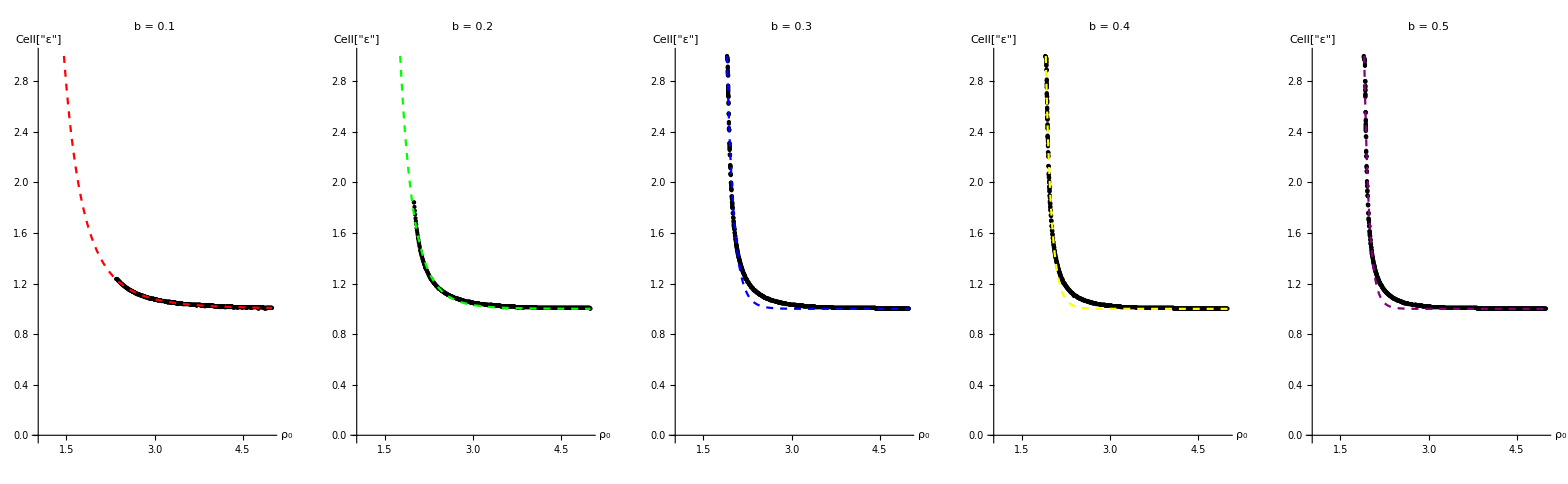

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn2Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn2⟦i⟧]
]
```

b = 0.1:  (1+11.0022/x^4.51897)

b = 0.2:  (1+169.629/x^7.85412)

b = 0.3:  (1+108092./x^16.949)

b = 0.4:  (1+721077./x^19.8326)

b = 0.5:  (1+(4.36838×10^6)/x^22.6423)

We see that this is a better fit. Next we try to fit the set of data to the expression  ε_esc= Exp(a/ρ_0). With this form, we still have ε_esc→ 1 as ρ_0→ ∞.

```mathematica
eqn3=Table[1+a/(x-r)+b/(x-r)^2/.FindFit[data⟦i⟧,1+a/(x-r)+b/(x-r)^2,{a,b,r},x],{i,1,5}];
eqn3Plot=Table[Plot[eqn3⟦i⟧,{x,First@First@data⟦i⟧,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

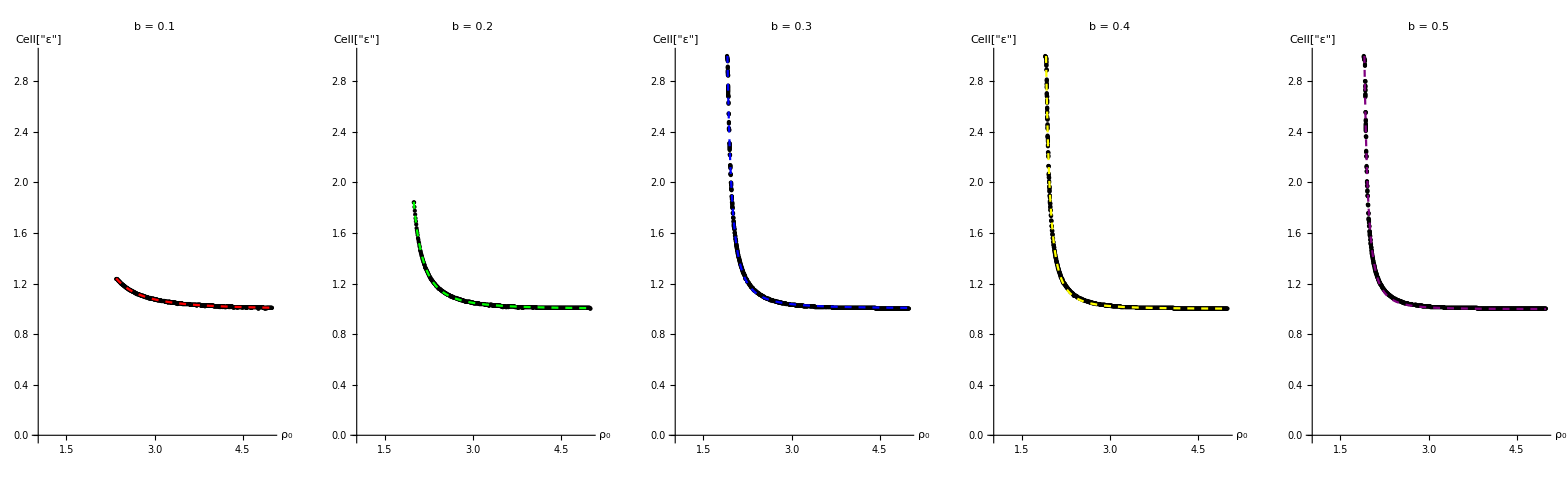

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn3Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn3⟦i⟧]
]
```

b = 0.1:  (1+0.259527/(-1.39136+x)^2-0.040513/(-1.39136+x))

b = 0.2:  (1+0.102317/(-1.65045+x)^2-0.0116653/(-1.65045+x))

b = 0.3:  (1+0.0430103/(-1.75951+x)^2+0.0116951/(-1.75951+x))

b = 0.4:  (1+0.0409488/(-1.76944+x)^2-0.00648885/(-1.76944+x))

b = 0.5:  (1+0.0355547/(-1.77887+x)^2-0.0149329/(-1.77887+x))

Very good fit!!

```mathematica
Export["Eescpl.png",Show[eqn3Plot,LabelStyle->{FontSize->60},ImageSize->2000]]
```

Eescpl.png

We try to obtain an approximate expression for the coefficients as a function of b

```mathematica
coeffDat={{{0.1,-0.040513},{0.2,-0.0116653},{0.3,0.0116951},{0.4,-0.00648885},{0.5,-0.0149329}},{{0.1,0.259527},{0.2,0.102317},{0.3,0.0430103},{0.4,0.0409488},{0.5,0.0355547}}};
```

```mathematica
poleDat={{0.1,1.39136},{0.2,1.65045},{0.3,1.75951},{0.4,1.76944},{0.5,1.77887}};
```

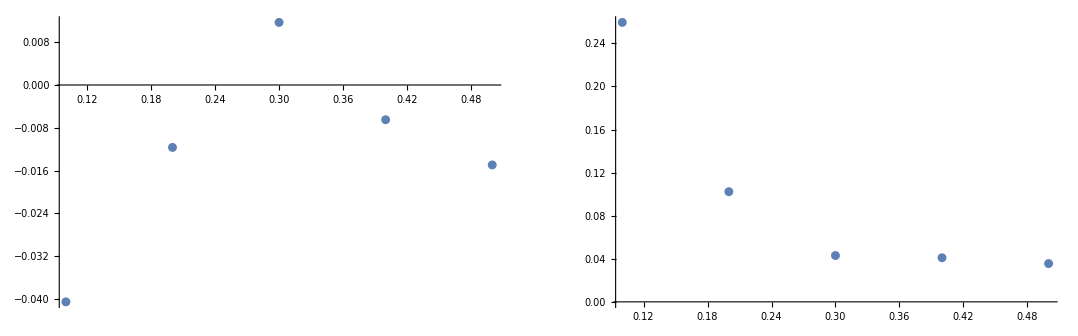

```mathematica
GraphicsRow[Table[ListPlot[coeffDat⟦i⟧,ImageSize->500],{i,1,2}]]
```

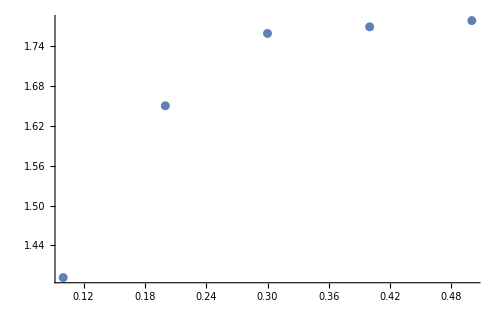

```mathematica
ListPlot[poleDat,ImageSize->500]
```

We attempt to write our approximate energy equation as
	ε_esc=(1+(α_1(b))/(ρ_0-γ(b))+(α_2(b))/(ρ_0-γ(b))^2)ε̄
where ε̄=1 for l>0 and ε̄=√(1+4 b |l|) for l<0, and use the fitting function
	f(b)=β_0+β_1 b+β_2 b^2
where f(b) stands for {α_1(b),α_2(b),γ(b)}.

```mathematica
eqn4=Table[a+c b+d b^2/.FindFit[coeffDat⟦i⟧,a+c b+d b^2 ,{a,c,d},b],{i,2}];
```

α_1(b) =  (-0.0873459+0.554027 b-0.829485 b^2)

α_2(b) =  (0.429504-2.05593 b+2.57769 b^2)

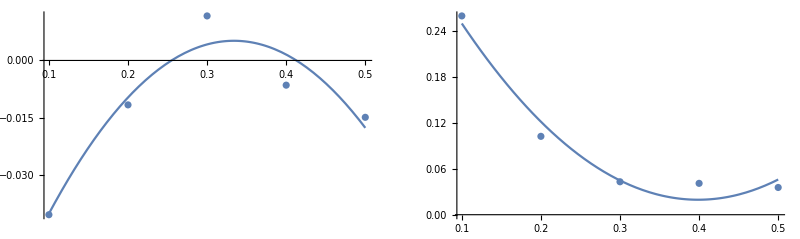

```mathematica
Print["α_1(b) = "eqn4⟦1⟧]
Print["α_2(b) = "eqn4⟦2⟧]
GraphicsRow[{Show[ListPlot[coeffDat⟦1⟧],Plot[eqn4⟦1⟧,{b,0.1,0.5}]],Show[ListPlot[coeffDat⟦2⟧],Plot[eqn4⟦2⟧,{b,0.1,0.5}]]},ImageSize->800]
```

```mathematica
AppendTo[eqn4,a+c b+d b^2/.FindFit[poleDat,a+c b+d b^2 ,{a,c,d},b]];
```

γ(b) =  (1.1025+3.4588 b-4.27464 b^2)

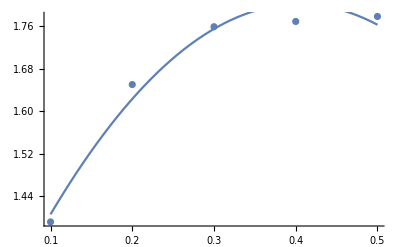

```mathematica
Print["γ(b) = "eqn4⟦3⟧]
Show[ListPlot[poleDat],Plot[eqn4⟦3⟧,{b,0.1,0.5}]]
```

We try to use third-order polynomial
	f(b)=β_0+β_1 b+β_2 b^2+β_3 b^3
to improve the fit

```mathematica
eqn5=Table[a+c b+d b^2+e b^3/.FindFit[coeffDat⟦i⟧,a+c b+d b^2+e b^3 ,{a,c,d,e},b],{i,2}]//Append[#,a+c b+d b^2+e b^3/.FindFit[poleDat,a+c b+d b^2+e b^3 ,{a,c,d,e},b]]&;
```

α_1(b) =  (-0.108664+0.853496 b-1.97152 b^2+1.26893 b^3)

α_2(b) =  (0.571234-4.0469 b+10.1704 b^2-8.43633 b^3)

γ(b) =  (0.893156+6.39955 b-15.4894 b^2+12.4608 b^3)

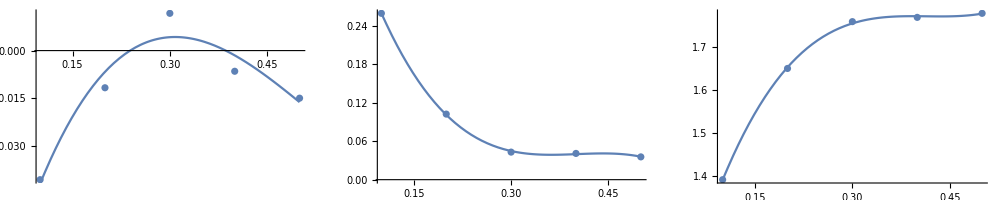

```mathematica
Print["α_1(b) = "eqn5⟦1⟧]
Print["α_2(b) = "eqn5⟦2⟧]
Print["γ(b) = "eqn5⟦3⟧]
GraphicsRow[{Show[ListPlot[coeffDat⟦1⟧],Plot[eqn5⟦1⟧,{b,0.1,0.5}]],Show[ListPlot[coeffDat⟦2⟧],Plot[eqn5⟦2⟧,{b,0.1,0.5}]],Show[ListPlot[poleDat],Plot[eqn5⟦3⟧,{b,0.1,0.5}]]},ImageSize->1000]
```

α_1(b) data doesn’t fit too well. Nevertheless, we choose this fit.

## Negative l

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\NegativeL"}]
```

{E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b01EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b02EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b03EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b04EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b05EscEdat.mx}

```mathematica
data=Import[#]&/@files;
```

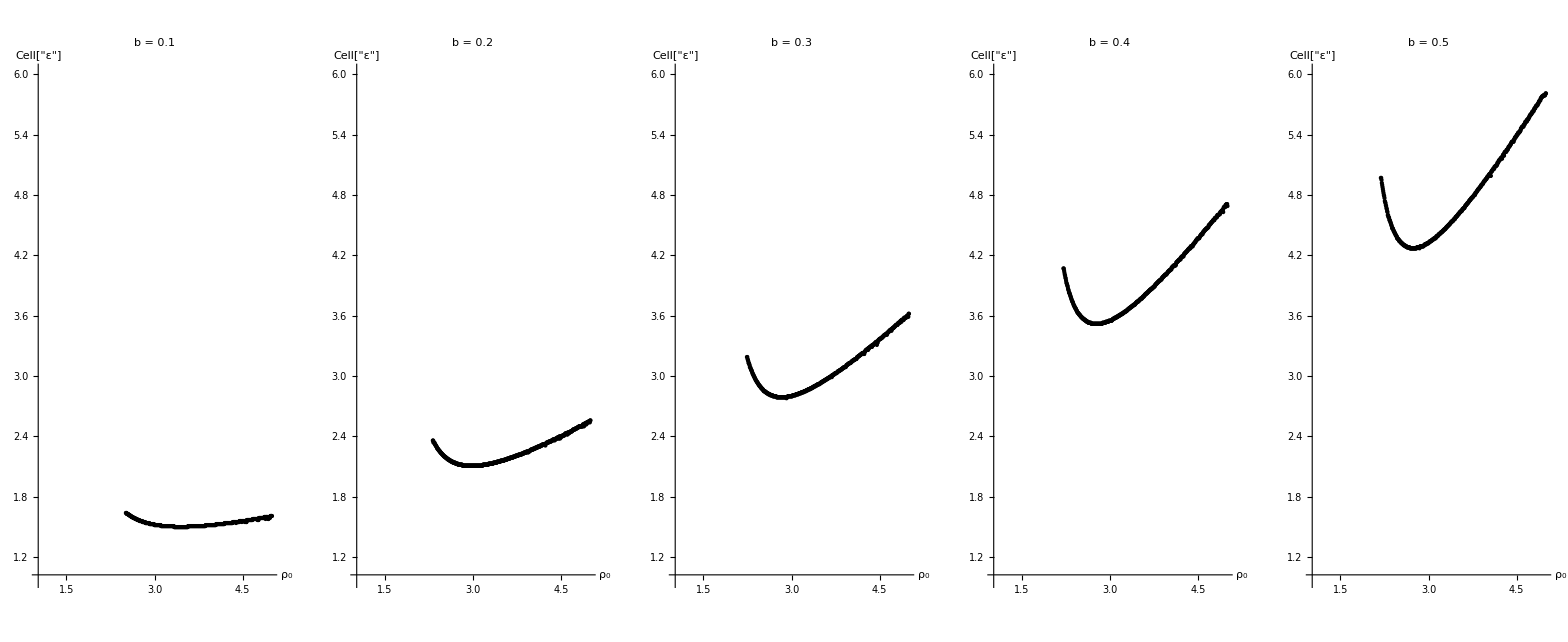

```mathematica
GraphicsRow[Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{1,6}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"d68ab53d-5fd5-4fda-a48d-866e977a9459"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->1],{i,1,5}]]
```

```mathematica
dataPlot=Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{1,6}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"c15653df-fc05-4c81-a186-bb306a6b9430"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->1],{i,1,5}];
```

```mathematica
plotColors={Red,Green,Blue,Yellow,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0.5, 0, 0.5]}

```mathematica
eqn=Table[Fit[data⟦i⟧,{1,1/x,1/x^2},x],{i,1,5}];
```

```mathematica
eqnPlot=Table[Plot[eqn⟦i⟧,{x,1,5},PlotRange->{{1,5},{1,6}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

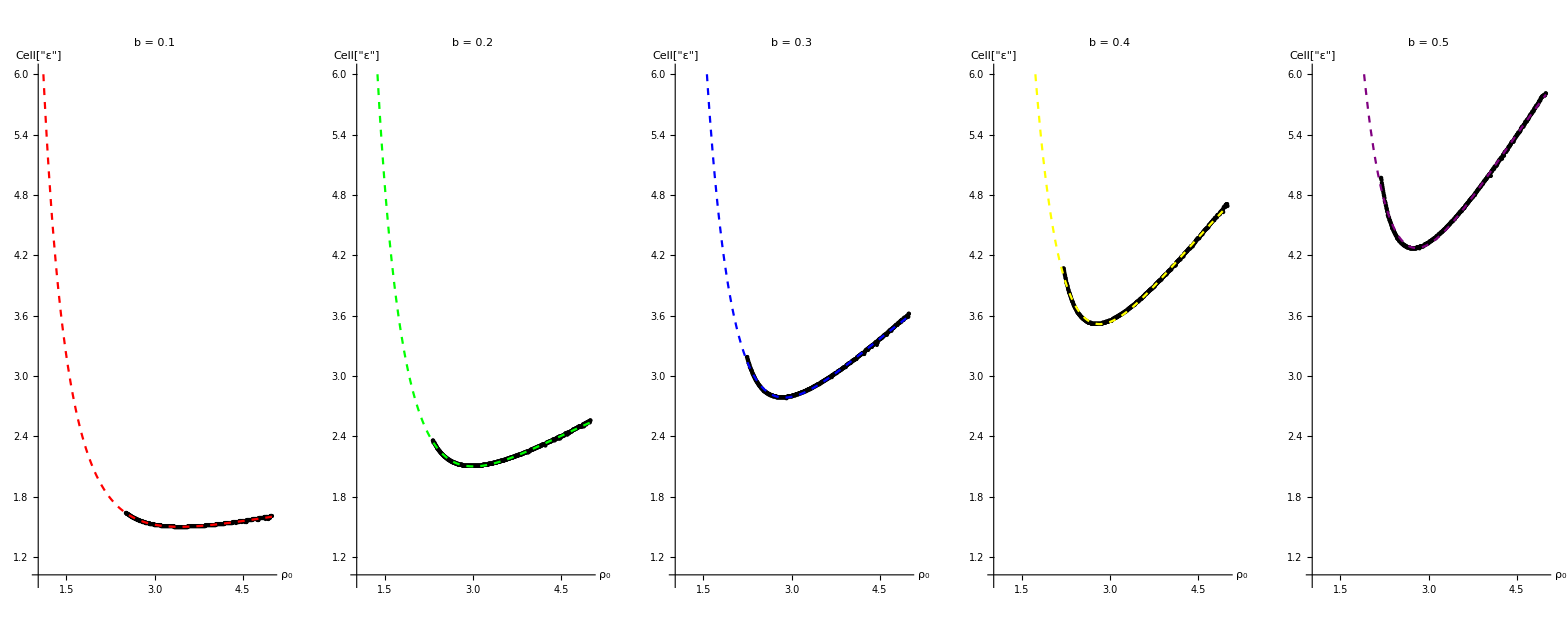

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqnPlot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn⟦i⟧]
]
```

b = 0.1:  (2.52302+12.0311/x^2-7.00817/x)

b = 0.2:  (4.85533+24.8838/x^2-16.5521/x)

b = 0.3:  (7.27755+37.2119/x^2-25.8539/x)

b = 0.4:  (9.70931+49.4048/x^2-34.9811/x)

b = 0.5:  (12.124+61.3671/x^2-43.8987/x)

We can see from above that the fit is quite accurate for negative l.

We try to another fit, taking into account that asymptotically (large ρ_0), the escape energy is

```mathematica
Ebar[b_]:=√(1+(4b)/(2x-3)(b x^2+x √(b^2 x^2-(3-2x)(b^2 x^2(2x-1)+1))));
```

```mathematica
eqn2=Table[(1+c/x+d/x^2)(Ebar[i/10])/.FindFit[data⟦i⟧,(1+c/x+d/x^2)(Ebar[i/10]),{c,d},x],{i,1,5}];
```

```mathematica
eqn2Plot=Table[Plot[eqn2⟦i⟧,{x,1,5},PlotRange->{{1,5},{1,6}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

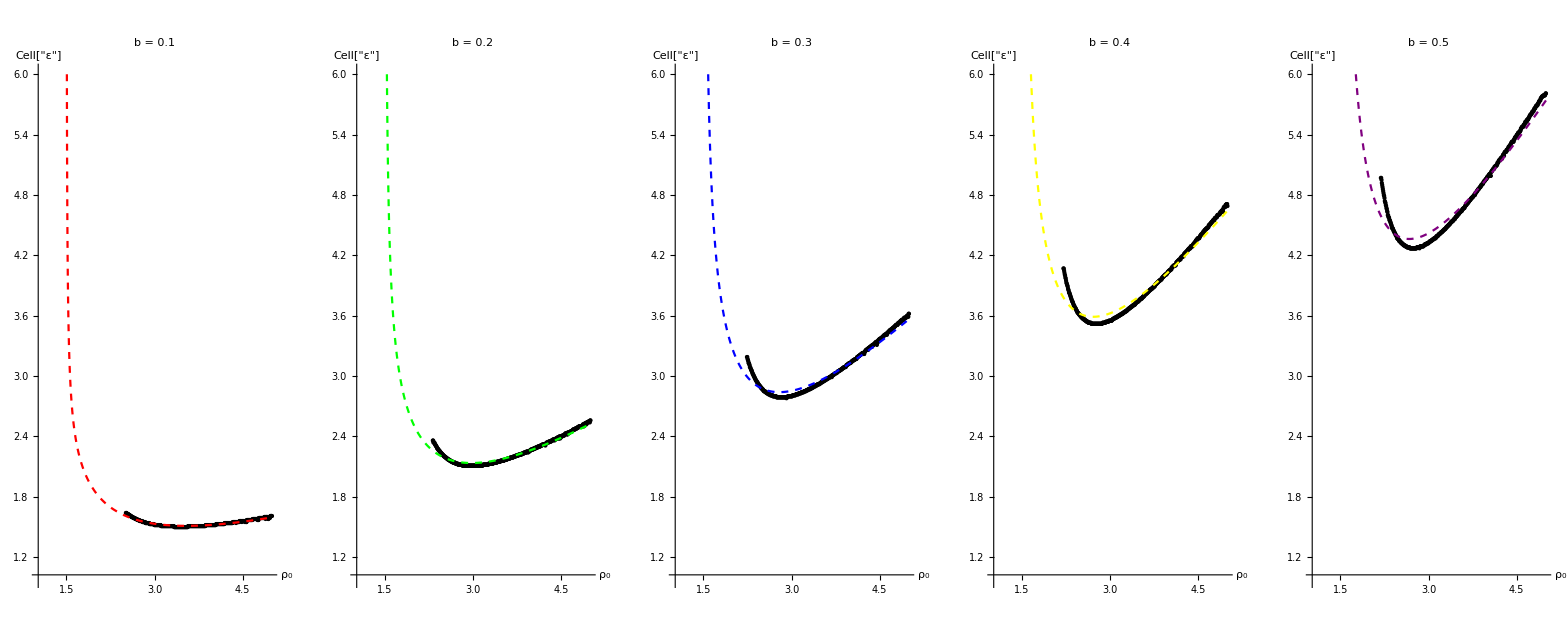

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn2Plot⟦i⟧],{i,1,5}]]
```

Try putting in a pole

```mathematica
eqn3=Table[(1+c/(x-r)+d/(x-r)^2)(Ebar[i/10])/.FindFit[data⟦i⟧,(1+c/(x-r)+d/(x-r)^2)(Ebar[i/10]),{c,d,r},x],{i,1,5}];
```

```mathematica
eqn3Plot=Table[Plot[eqn3⟦i⟧,{x,1,5},PlotRange->{{1,5},{1,6}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

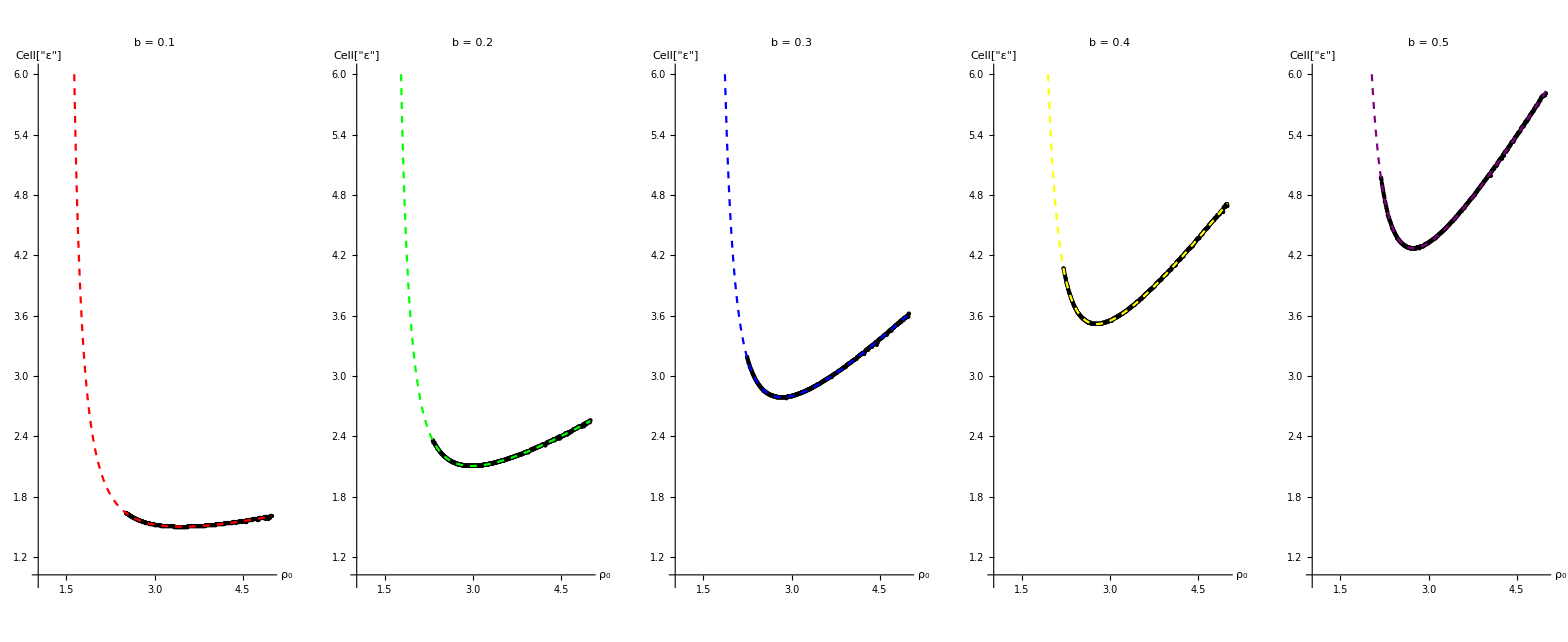

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn3Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn3⟦i⟧]
]
```

b = 0.1:  (1+0.306305/(-1.29683+x)^2-0.0298235/(-1.29683+x)) √(1+(2 (x^2/10+x √(x^2/100-(3-2 x) (1+1/100 x^2 (-1+2 x)))))/(5 (-3+2 x)))

b = 0.2:  (1+0.213559/(-1.44492+x)^2-0.0218701/(-1.44492+x)) √(1+(4 (x^2/5+x √(x^2/25-(3-2 x) (1+1/25 x^2 (-1+2 x)))))/(5 (-3+2 x)))

b = 0.3:  (1+0.175829/(-1.50806+x)^2-0.0153949/(-1.50806+x)) √(1+(6 ((3 x^2)/10+x √((9 x^2)/100-(3-2 x) (1+9/100 x^2 (-1+2 x)))))/(5 (-3+2 x)))

b = 0.4:  (1+0.16277/(-1.53077+x)^2-0.0135345/(-1.53077+x)) √(1+(8 ((2 x^2)/5+x √((4 x^2)/25-(3-2 x) (1+4/25 x^2 (-1+2 x)))))/(5 (-3+2 x)))

b = 0.5:  (1+0.158149/(-1.53768+x)^2-0.0131803/(-1.53768+x)) √(1+(2 (x^2/2+x √(x^2/4-(3-2 x) (1+1/4 x^2 (-1+2 x)))))/(-3+2 x))

```mathematica
coeffDat2={{{0.1,-0.0328235},{0.2,-0.0218701},{0.3,-0.0153949},{0.4,-0.0135345},{0.5,-0.0131803}},{{0.1,0.306305},{0.2,0.213559},{0.3,0.175829},{0.4,0.16277},{0.5,0.158149}}};
poleDat2={{0.1,1.29683},{0.2,1.44492},{0.3,1.50806},{0.4,1.53077},{0.5,1.53768}};
```

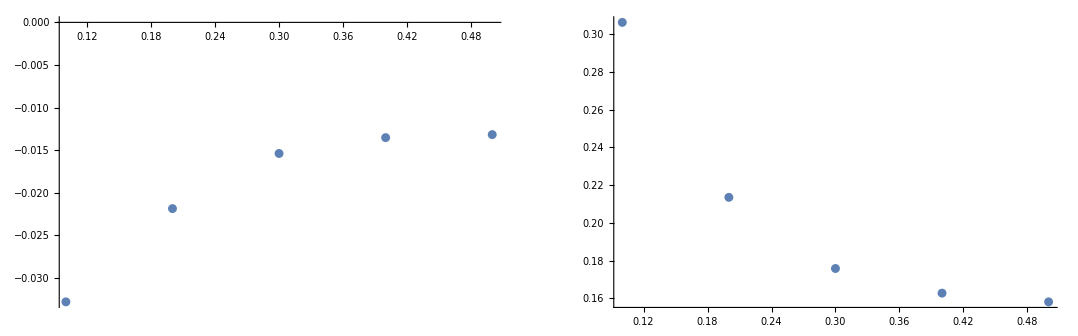

```mathematica
GraphicsRow[Table[ListPlot[coeffDat2⟦i⟧,ImageSize->500],{i,1,2}]]
```

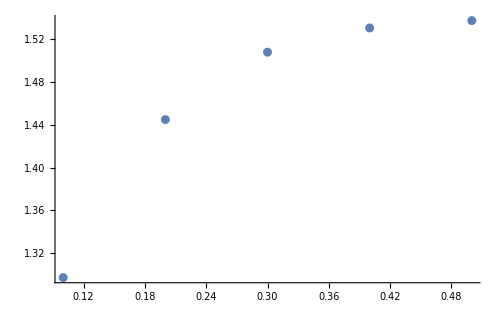

```mathematica
ListPlot[poleDat2,ImageSize->500]
```

We also use a third-order polynomial fit here
	f(b)=β_0+β_1 b+β_2 b^2+β_3 b^3

```mathematica
eqn6=Table[a+c b+d b^2+e b^3/.FindFit[coeffDat2⟦i⟧,a+c b+d b^2+e b^3 ,{a,c,d,e},b],{i,2}]//Append[#,a+c b+d b^2+e b^3/.FindFit[poleDat2,a+c b+d b^2+e b^3 ,{a,c,d,e},b]]&;
```

α_1(b) =  (-0.0507147+0.216699 b-0.40728 b^2+0.247667 b^3)

α_2(b) =  (0.473122-2.12423 b+4.9285 b^2-3.8815 b^3)

γ(b) =  (1.03518+3.31089 b-7.49189 b^2+5.7625 b^3)

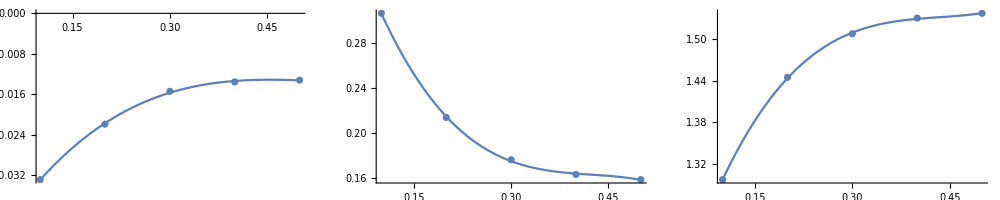

```mathematica
Print["α_1(b) = "eqn6⟦1⟧]
Print["α_2(b) = "eqn6⟦2⟧]
Print["γ(b) = "eqn6⟦3⟧]
GraphicsRow[{Show[ListPlot[coeffDat2⟦1⟧],Plot[eqn6⟦1⟧,{b,0.1,0.5}]],Show[ListPlot[coeffDat2⟦2⟧],Plot[eqn6⟦2⟧,{b,0.1,0.5}]],Show[ListPlot[poleDat2],Plot[eqn6⟦3⟧,{b,0.1,0.5}]]},ImageSize->1000]
```

## Fitting using the coefficients

Now we try to fit the escape energy data using these coefficients:

```mathematica
Print["l>0"]
Print["α_1(b) = "eqn5⟦1⟧]
Print["α_2(b) = "eqn5⟦2⟧]
Print["γ(b) = "eqn5⟦3⟧]
```

l>0

α_1(b) =  (-0.108664+0.853496 b-1.97152 b^2+1.26893 b^3)

α_2(b) =  (0.571234-4.0469 b+10.1704 b^2-8.43633 b^3)

γ(b) =  (0.893156+6.39955 b-15.4894 b^2+12.4608 b^3)

```mathematica
Print["l<0"]
Print["α_1(b) = "eqn6⟦1⟧]
Print["α_2(b) = "eqn6⟦2⟧]
Print["γ(b) = "eqn6⟦3⟧]
```

l<0

α_1(b) =  (-0.0507147+0.216699 b-0.40728 b^2+0.247667 b^3)

α_2(b) =  (0.473122-2.12423 b+4.9285 b^2-3.8815 b^3)

γ(b) =  (1.03518+3.31089 b-7.49189 b^2+5.7625 b^3)

```mathematica
α1[b_]:=If[$IsPositive,-0.10866399000000043+0.8534957023809533 b-1.971524642857145 b^2+1.2689333333333404 b^3,-0.050714660000000196+0.21669933333333416 b-0.4072800000000025 b^2+0.24766666666667103 b^3];
α2[b_]:=If[$IsPositive,0.5712341600000023-4.046901214285725 b+10.170385357142893 b^2-8.436325000000055 b^3,0.47312240000000194-2.124225000000011 b+4.9285000000000325 b^2-3.8815000000000457 b^3];
γ[b_]:=If[$IsPositive,0.8931560000000002+6.399552380952379 b-15.48939285714286 b^2+12.460833333333355 b^3,(1.0351819999999994+3.3108857142857206 b-7.491892857142881 b^2+5.7625000000000215 b^3)];
```

```mathematica
Ebar[b_]:=If[$IsPositive,1,√(1+(4b)/(2x-3)(b x^2+x √(b^2 x^2-(3-2x)(b^2 x^2(2x-1)+1))))];
```

```mathematica
escEn[b_]:=(1+α1[b]/(x-γ[b])+α2[b]/(x-γ[b])^2)*Ebar[b];
```

```mathematica
plotColors={Red,Green,Blue,Orange,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5]}

```mathematica
bvalues={0.1,0.2,0.3,0.4,0.5};
```

Positive l

```mathematica
$IsPositive=True;
```

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\PositiveL"}];
```

```mathematica
datapl=Import[#]&/@files;
```

```mathematica
dataplPlot=Table[ListPlot[datapl⟦i⟧,PlotRange->{{1.8,5},{0,3}},PlotStyle->{plotColors⟦i⟧//Lighter,PointSize[0.001]},Frame-> True,LabelStyle->Directive[Black, 14],FrameLabel->{Style["ρ_0",18],Style["ε",18]},RotateLabel->False,ImageSize->500],{i,5}];
```

```mathematica
analyticplPlot=Table[Plot[escEn[bvalues⟦i⟧],{x,1.8,5},PlotRange->{{1,5},{0,3}},PlotStyle->Directive[plotColors⟦i⟧//Darker,Dashed,Thickness[0.003]],Frame-> True,LabelStyle->Directive[Black, 14],FrameLabel->{Style["ρ_0",18],Style["ε",18]},RotateLabel->False,ImageSize->500],{i,5}];
```

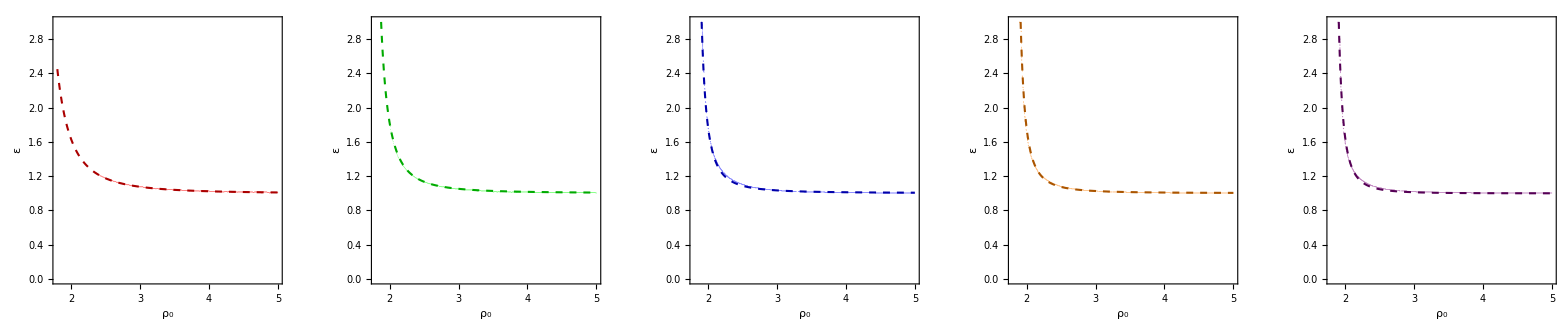

```mathematica
GraphicsRow[Table[Show[dataplPlot⟦i⟧,analyticplPlot⟦i⟧],{i,5}]]
```

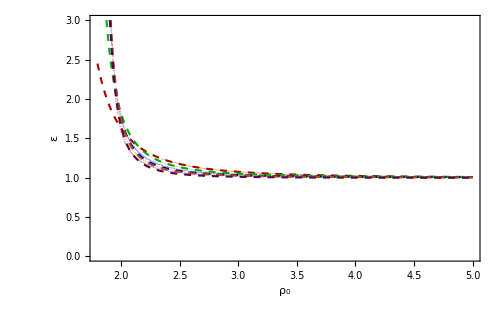

```mathematica
Show[dataplPlot~Join~analyticplPlot]
```

Negative l

```mathematica
$IsPositive=False;
```

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\NegativeL"}];
datanl=Import[#]&/@files;
```

```mathematica
datanlPlot=Table[ListPlot[datanl⟦i⟧,PlotRange->{{2.15,5},{0,6}},PlotStyle->Directive[plotColors⟦i⟧//Lighter,PointSize[0.001]],Frame-> True,LabelStyle->Directive[Black, 14],FrameLabel->{Style["ρ_0",18],Style["ε",18]},RotateLabel->False,ImageSize->500],{i,5}];
analyticnlPlot=Table[Plot[escEn[bvalues⟦i⟧],{x,2.15,5},PlotRange->{{1,5},{0,6}},PlotStyle->Directive[plotColors⟦i⟧//Darker,Thickness[0.003],Dashed],Frame-> True,LabelStyle->Directive[Black, 14],FrameLabel->{Style["ρ_0",18],Style["ε",18]},RotateLabel->False,ImageSize->500],{i,5}];
```

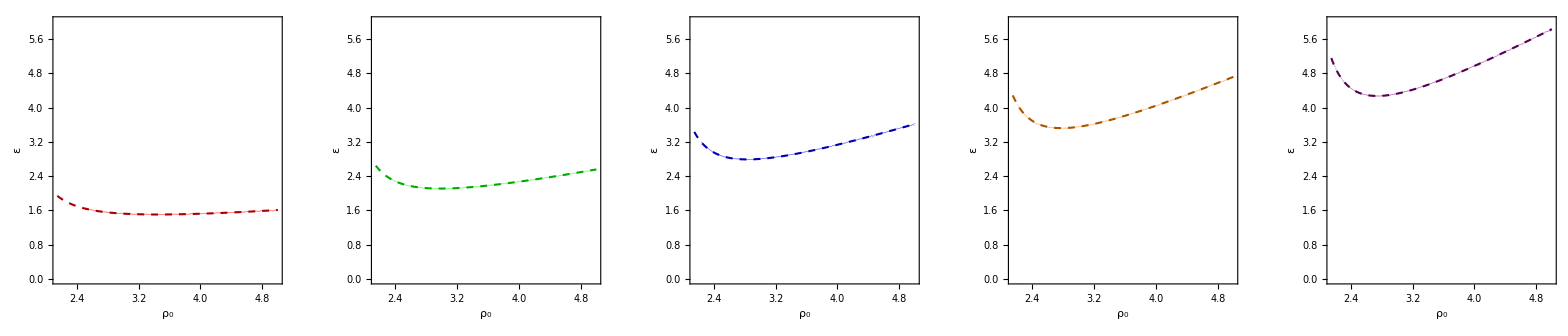

```mathematica
GraphicsRow[Table[Show[datanlPlot⟦i⟧,analyticnlPlot⟦i⟧],{i,5}]]
```

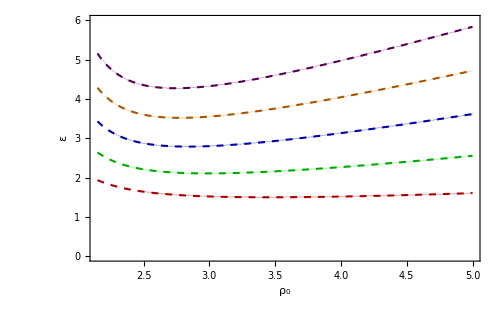

```mathematica
Show[datanlPlot~Join~analyticnlPlot]
```